# Indice de los temas

Tema 1 -> Ver las acotaciones de un complejo .
    Tema 2 -> Números complejos "PARTE TOTALMENTE TEORICA" .
     	Tema 3 -> Calculo de sucesiones tanto limites como si converge .
      		Tema 4 -> Funciones Reales .
       			Tema 5 -> Derivadas .
        				Tema 6 -> Integrales .
        					Tema7 -> Series .
          						Tema 8 -> Funciones de Varias Variables .
          							Tema 9-> Ecuaciones diferenciales
          								Tema 10 y 13->Métodos de Euler,Taylor y Runge-Kutta
          									Tema 11  -> Métodos de Newton , bisecciones y método secante
          										Tema 12->Deducción de formulas

## Tema 1

#### Estudia el conjunto de los x que cumplen 7 - 6 x + x^3 >= 7 - x^2

SU FUNCION SERIA -> Reduce[la ecuación, la incognita]

```mathematica
Reduce[7-6x+x^3≥ 7-x^2,x]
```

-3≤x≤0||x≥2

Solución :
Conjunto Solución :   [-3, 0] ∪ [2, ∞)                            
Acotado superior :  NO                             Acotado Inferior : SI
Máximo :        NO            Mínimo :      -3           Supremo :      NO              Ínfimo : -3

#### Estudia el conjunto de los x que cumplen 6-5 y+y^3<2+y.

SU FUNCION SERIA -> Reduce[la ecuación, la incognita]

```mathematica
Reduce[6-5 y+y^3<2+y,y]
```

y<-1-√3||-1+√3<y<2

El resultado que nos da el Mathematica nos indica que el conjunto solución de esta inecuación es(-∞, -1-√3)  U   (-1+√3,2).  Es un conjunto acotado superiormente,pero no tiene corta inferior.No tiene máximo,ni mínimo.Tiene supremo que es el 2,pero no pertenece al conjunto,por eso no es el máximo.

#### Estudiar el conjunto de los números reales que cumplen x - | x - 1 | 0 < 1.

Cuando tengamos un valor absoluto usaremos la función Abs[la parte absoluta]

```mathematica
Reduce[x -Abs[x - 1 ]< 1,x]
```

x<1

La solución sería x < 1

#### 1.Calcular el conjunto de los x que cumplen 6-5x + x^3 <2+x.Decir si es acotado superior o interiormente, si tiene supremo o ínfimo, máximo o minino, indicando sus valores.

```mathematica
Reduce[6-5x+x^3<2+x,x]
```

x<-1-√3||-1+√3<x<2

El resultado nos indica que el conjunto solucion de esta inecuacion es (-∞,-1-√3)U (-1-√3,2)
Esta acotado superiormente. No tiene cota inferior 
No tiene maximo o minimo 
El supremo del conjunto es 2 y no tiene infimo

## Tema 3

#### 1. Calcular el limite de una sucesión {(n^2 + cos(n))/(1 + 2 + 3 + ... + n)}

```mathematica
Limit[(∑_(i=1)^n n^2+Cos[n])/(1+n), n->∞]
```

∞

#### 2.Calcular el límite de la sucesión{(1^2 + 2^2 + 3^2 + ... + n^2)/(n^3+1)}

```mathematica
Limit[(∑_(i=1)^n n^2)/(n^3+1), n->∞]
```

1

#### 3.Calcular el límite de la sucesión {(n^2+3)/2^n}

```mathematica
Limit[(∑_(i=1)^n n^2+3)/2^n, n->∞]
```

0

#### 4.Estudiar la convergencia de la sucesión{(1+3+5+7+...+(2n+1))/n^2} .

```mathematica
Limit[(∑_(i=1)^n n+2n+1)/n^2, n->∞]
```

1

#### 5.El límite de la sucesión{(3/2*6/8*...*(n^2+ 2)/(2 n^2))^(1/n)}es:

```mathematica
Limit[(3/2*6/8)^(1/n)*(n+2)/(2n),n->∞]
```

1/2

#### 6.El límite de la sucesión {(2/3*5/9*...*(n^2+ 1)/(2 n^2+1))^(1/n)} es:

```mathematica
Limit[(∏_(i=1)^n (n^2+ 1)/(2 n^2+1))^(1/n),n->Infinity]
```

1/2

## Tema 4

#### Información:

Nosotros en Mathematica podemos definir funciones llamándolas f[x_] : al valor que queramos .

```mathematica
ClearAll
```

ClearAll

```mathematica
f1[x_]:= Sin[x-2]
```

```mathematica
f1[0]
```

-Sin[2]

Podemos hacer una serie y saber los decimales en este caso haremos el ejemplo del 1 al 4.

```mathematica
{f1[0],f1[1],f1[2],f1[3],f1[4]}//N
```

{-0.909297,-0.841471,0.,0.841471,0.909297}

Si nos piden una representación grafica podemos usar :

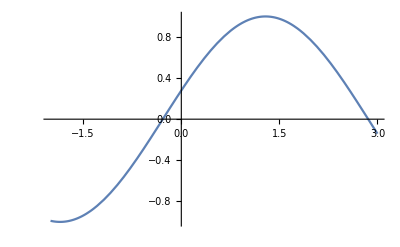

```mathematica
Plot[f[x],{x,-2,3}]
```

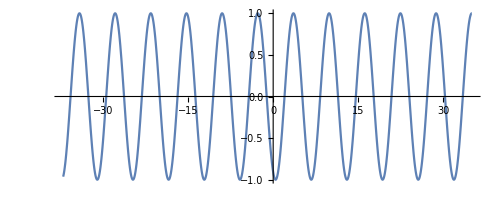

```mathematica
Plot[f1[x],{x,-37,35},AspectRatio->Automatic]
```

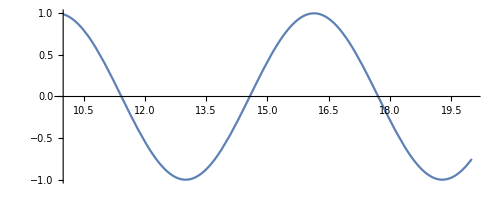

```mathematica
Plot[f1[x],{x,10,20},AspectRatio->All]
```

Limites

```mathematica
Limit[3x^2+4x+2,x->Infinity]
```

∞

```mathematica
Limit[3x^2+4x+2,x->0]
```

2

```mathematica
Limit[Cos[1/x],x->0]
```

Indeterminate

#### 1.) Estudie el Signo de la función f (y) = (y^2 - 4)/(y^4 - y^2)

Recuerde que en como es una fracción el único problema que tendríamos al estudiar su signo seria que el denominador se anulase .

```mathematica
Solve[(y^2-4)/(y^4-y^2)==0,y]
```

{{y→-2},{y→2}}

#### 2.) Estudie el Signo de la función f(x) =|x^2-1|

```mathematica
Solve[Abs[x^2-1]==0,x]
```

{{x→-1},{x→1}}

#### 3.) El conjunto de las soluciones de la ecuación |(x+1)/(x-1)|≤4.

```mathematica
Reduce[Abs[(x+1)/(x-1)]<=4,x,Reals]
```

x≤3/5||x≥5/3

1)  Está acotado superiormente 2) Tiene máximo absoluto, 3) Tiene cota inferior,  4) No tiene mínimo, 5) No tiene soluciones

#### 4.El conjunto de las soluciones de la ecuación |(x-1)/(x+1)|<4. Está acotado superiormente 2) Tiene máximo absoluto, 3) No tiene cota inferior, 4)Tiene mínimo, 5) No tiene soluciones

```mathematica
Reduce[Abs[(x-1)/(x+1)]<4,x,Reals]
```

x<-5/3||x>-3/5

## Tema 5

#### 1.Calcular los máximos y mínimos absolutos de la función f(x) =x^3-3 x^2+2 en el intervalo [1, 3].

Gráficamente la evaluaríamos de la siguiente manera -> Plot[ecuacion,{x,punto a evaluar 1, punto a evaluar 2}]

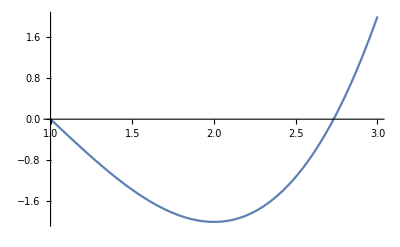

```mathematica
Plot[x^3-3 x^2+2,{x,1,3}]
```

Si queremos evaluarla en los puntos debemos hacer la derivada de la f (x) e igualarla a 0

```mathematica
D[x^3-3 x^2+2]
```

2-3 x^2+x^3

Igualamos a 0.

```mathematica
Solve[2-3 x^2+x^3==0,x]
```

{{x→1},{x→1-√3},{x→1+√3}}

```mathematica
Y sustituimos en los puntos 1,3
```

```mathematica
f[x_]:=2-3 x^2+x^3
```

```mathematica
f[1]
```

0

```mathematica
f[3]
```

2

El máximo seria en x = 3 con valor de 2 y el minino en x = 1 con valor de 0.

## Tema 6

#### 1. Como descomponer en fracciones simples .

```mathematica
Apart[3x^2+3/x^3-x]
```

3/x^3-x+3 x^2

#### 2. Calculo del área de una superficie de revolución,dada una función f(x) = sen x en el intervalo [0,π], consideramos su gráfica

1. Paso : Definimos la función

```mathematica
f[x_]:=Sin [x]
```

2. Paso: Hacemos la representación Gráfica

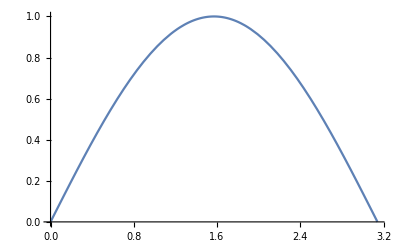

```mathematica
Plot[f[x],{x,0,Pi}]
```

3. Paso : Calcular el superficie exterior que viene dada por una integral

```mathematica
∫_0^π 2π f[x] √(1+f'[x]^2)ⅆx
```

2 π (√2+ArcCoth[√2])

4. Paso : Si queremos el valor numérico en Mathematica usamos el % para sacar los últimos valores

```mathematica
N[%]
```

14.4236

#### 3. Calcula la integral de la función f(x,y)=x^2+2y^2 en el cuadrilátero de vertices (0,0),(1,0),(2,1),(1,1)

Tenemos que calcular la integral de la función f (x, y) en el dominio D = {(x, y)/0 <= y <= 1 , y <= x <= y + 1 } Luego los limites de la integral seran (0, 1) para la variable y, (y, y + 1) para la variable x

```mathematica
∫_0^1 ∫_y^(y+1) (x^2+2y^2)ⅆxⅆy
```

11/6

#### 4.Calcula la integral de la funcion f(x,y)=1-x-y en el triangulo de vertices (0,0),(1,0),(0,1) para obtener el volumen de la siguiente figura

Tenemos que calcular la integral de la funcion f (x, y) en el dominio D = {(x, y)/0<=x<=1,0<=y<=1-x } Luego los limites de la integral seran (0, 1) para la variable x, (0,1-x) para la variable y

```mathematica
∫_0^1 ∫_0^(1-x) (1-x-y)ⅆyⅆx
```

1/6

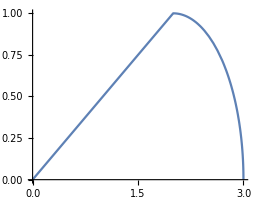
#### 5. Calcular el volumen de la peonza formada por una semiesfera de radio 1 y un cono de altura 2 y radio 1, según aparece en la gráfica. -Graphics- -Graphics3D-

```mathematica
f[x_]:= Which[0<=x<=2,x/2,2<=x<=3,√(1-(x-2)^2)]
Integrate[Pi f[x]^2,{x,0,3}]//N
```

4.18879

#### 6. Calcular la superficie de la peonza formada por una semiesfera de radio 1 y un cono de altura 2 y radio 1, según aparece en la gráfica. -Graphics- -Graphics3D- El segundo decimal es: 1) 1, 2) 0, 3) 5, 4) 8, 5) 6

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]:=Which[0<=x<=2,x/2,2<=x<=3,√(1-(x-2)^2)]
```

```mathematica
Integrate[2Pi f[x] Sqrt[1+f'[x]^2],{x,0,3}]//N
```

13.308

## Tema 7

#### 1. Calcular la suma de la serie ∑_(n=1)^Infinity (2n+1)/3^n

Para este tema debemos tener unos términos claros para que nos sea útil realizar los ejercicios .

1. Paso : Definimos la suma inicial .

```mathematica
f[x_]:=(2n+1)/3^n
```

2. Paso : Evaluar la suma de {n = 1} a {n = ∞} usando la función del Mathematica Sum[función,{n,intervalo inicial,intervalo final}]

```mathematica
Sum[f[n],{n,1,Infinity}]
```

2

#### 2. Calcular una serie de estas 4 series : ∑_(n=1)^Infinity (2n+1)/3^n , ∑_(n=1)^6 (4n+1)/Sin[n+9n], ∑_(n=1)^87 Pi/n , ∑_(n=1)^Infinity (2*Pi)+1

1. Paso : Definimos cada serie una por una en una función .

```mathematica
a[x_]:=(2n+1)/3^n
b[x_]:=(4n+1)/Sin[n+9n]
c[x_]:=Pi/n
d[x_]:=(2*Pi)+1
```

2. Paso . Evaluar y hacer la formula {a[n], b[n], ..., n[n]} // N

```mathematica
{∑_(n=1)^Infinity a[n],∑_(n=1)^6 b[n],∑_(n=1)^87 c[n],∑_(n=1)^Infinity d[n]}//N
```

Sum::div: Sum does not converge.

{2.,-151.731,15.8615,ComplexInfinity}

#### 3.- Calcular la suma de la serie ∑_(n=5)^∞ 4/(n^2-1).

1. Paso : Definimos la suma inicial .

```mathematica
s[x_]:=4/(n^2-1)
```

2. Paso : Evaluar la suma de {n = 1} a {n = ∞} usando la función del Mathematica Sum[función, {n, intervalo inicial, intervalo final}]

```mathematica
Sum[s[n],{n,5,Infinity}]
```

9/10

## Tema 8

#### 1.Calcular si existe el límite de la función f(x,y)=(3x-2y)/(x^2+ y^2)en el infinito.

1 .ba Paso : Definir la función en los puntos que nos pidan .

```mathematica
f[n_ ,y_]:=(3x-2y)/(x^2+ y^2)
```

2. Paso : Cambiamos a polares

```mathematica
x:= p Cos a
y:=p Sin a
```

```mathematica
(3x-2y)/(x^2+ y^2)
```

(3 a Cos p-2 a p Sin)/(a^2 Cos^2 p^2+a^2 p^2 Sin^2)

3. Paso : Simplificamos la función al máximo

```mathematica
Simplify[(3x-2y)/(x^2+ y^2)]
```

(3 Cos-2 Sin)/(a Cos^2 p+a p Sin^2)

4. Paso :  Y calculamos el limite .

```mathematica
Limit[%,Infinity]
```

/*En caso de que se produzca un error puedes hacerlo a mano gracias a la simplificación*/

#### 2.Calcular si existe el límite de la función f(x,y)=(x^3+y^3)/(x^2+y^2)en el punto (0,0).

1 .ba Paso : Definir la función en los puntos que nos pidan .

```mathematica
l[x_,y_]:=(x^3+y^3)/(x^2+y^2)
```

2. Paso : Cambiamos a polares

```mathematica
x:= p Cos a
y:=p Sin a
```

3. Paso : Simplificamos la función al máximo

```mathematica
Simplify[l[x,y]]
```

(a p (Cos^3+Sin^3))/(Cos^2+Sin^2)

4. Paso :  Y calculamos el limite .

En (0, 0)

#### 3.- Calcular los extremos relativos (máximos, mínimos y puntos de silla) de la función f(x,y)=x^3+2 y^2-3x+4.

1 .ba Paso : Definirla en Mathematica

```mathematica
ClearAll
```

ClearAll

```mathematica
f[x_,y_]:=x^3+2 y^2-3x+4
```

2.baPaso: Derivar en la df/dx,df/dy

```mathematica
dx[x_]:=D[x^3-3x+4d]
```

```mathematica
dy[y_]:=D[+2 y^2+4]
```

3 .baPaso igual la función a 0 para sacar raíces y evaluar en esos puntos

```mathematica
Hessiano (dx_,dy_) := |({{D[dx], D[dx*dy])}, {D[dx*dy]), D[dy](x,y)}})|
```

## Tema 9

Este tema es muy sencillo ya que el Mathematica es capaz de estudiar a través del comando DSolve la ecuación diferencial ->DSolve[{ ecuación, condición1, condición2, ... }, y[x], x]

#### 1.Resolver la ecuación diferencial y' - 2y es y(x)= x + e^x.

```mathematica
DSolve[y'[x]==2y[x],y[x],x]
```

{{y[x]→ⅇ^(2 x) C[1]}}

```mathematica
DSolve[{y'[x]==2y[x],y[0]==1000},y[x],x]
```

{{y[x]→1000 ⅇ^(2 x)}}

#### 2. Dado el problema de valores iniciales y' = 2 y (20 - y) con y (G) = M, escribir y (G + 1) con 8 cifras decimales . (G ) y M son ciertas cifras de vuestro DNI

1 .ba Paso hacer la ecuación diferencial con la función DSolve

```mathematica
DSolve[y'[x]==2y[x](20-y[x]),y[x],x]
```

{{y[x]→(20 ⅇ^(40 x))/(ⅇ^(40 x)+ⅇ^(20 C[1]))}}

Ya tenemos una solución particular

```mathematica
Resolvemos cuando G=Dni
```

```mathematica
G=77433388;
M=77433388;
```

```mathematica
DSolve[{y'[x]==2y[x](20-y[x]),y[G]==M},y[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→(20 ⅇ^(40 x))/(-(19358342 ⅇ^3097335520)/19358347+ⅇ^(40 x))}}

#### 3. Dado el problema de valores iniciales y' = 2 y (20 - y) con y (0) = 1, escribir y (0.1) con 8 cifras decimales .

```mathematica
DSolve[{y'[x]==2 y[x](20-y[x]),y[0]==1},y[x],x]
```

{{y[x]→(20 ⅇ^(40 x))/(19+ⅇ^(40 x))}}

```mathematica
N[(20 ⅇ^4)/(19+ⅇ^4),10]
```

14.83682674

#### 4. La temperatura de un cuerpo que se está enfriando se aproxima por la solución de la ecuación diferencial y' = K (20 - y), para una cierta constante K, sabiendo que y (0) = 40 e y (2) = 30, calcular y (5) .

```mathematica
ClearAll
```

ClearAll

```mathematica
DSolve[{y'[x]==k (20-y[x]),y[0]==40},y[x],x]
```

{{y[x]→20 ⅇ^(-k x) (1+ⅇ^(k x))}}

```mathematica
Solve[20 ⅇ^(-2k) (1+ⅇ^(2k))==30,k]
```

{{k→ConditionalExpression[1/2 (2 ⅈ π C[1]+Log[2]), C[1]∈ℤ]}}

```mathematica
k=1/2 (Log[2])
```

Log[2]/2

```mathematica
20 ⅇ^(-k x) (1+ⅇ^(k x))/.x->5//Simplify
```

5/2 (8+√2)

```mathematica
N[%]
```

23.5355

#### 5.- Determinar los valores del parámetro m para los que la función h(x) = x^m es una solución de la ecuación diferencial x^2 y'' - 7xy' + 15 y = 0.

Se podría sustituir en la ecuación la función h(x)=x^m y encontrar cuándo es solución:
Si h(x) =x^m, h’(x)= m x^(m-1), h’’(x)=m(m-1) x^(m-2). (Los casos m=0 o 1, se pueden estudiar aparte)

x^2m(m-1) x^(m-2)  - 7xm x^(m-1) + 15 x^m = m(m-1) x^m  - 7m x^m + 15 x^m = (m(m-1)  - 7m + 15 )x^m=0 cuando  m(m-1)  - 7m + 15=0, resolviendo esta ecuación m^2  - 8m + 15=0, encontramos, m=5 ó 3. 

Otra posibilidad es, utilizando el Mathematica, resolver la ecuación de partida y ver las posibles soluciones.

```mathematica
DSolve[x^2 y''[x]-7 x y'[x] +15 y[x]==0,y[x],x]
```

{{y[x]→x^3 C[1]+x^5 C[2]}}

#### 6.Calcular una aproximacion de la integral de∫_0^1 1/(1+x+x^2)ⅆx utilizando la formula del trapecio compuesta haciendo 10 trozos en el intervalo[0,1]

```mathematica
Clear[f,x,a,b,n,xx]
f[x_]:=1/(1+x+x^2)
a=0;
b=1;
n=10;
xx=Table[a+i(b-a)/n,{i,0,n}];
trapC=(b-a)/n∑_(i=1)^n (f[xx[[i]]]+f[xx[[i+1]]])/2;
N[{∫_a^b f[x]ⅆx,trapC},10]
```

{0.6045997881,0.6051562695}

## Tema 10 y 13

### Método de Euler :

DATOS DE LA OPERACIÓN :

```mathematica
f[x_,y_]:=Sin[x]*Cos[x]-y*Cos[x]
a=0.;
b=2Pi;
yy[0]=1;
n=20;
h=(b-a)/n;
xx[i_]:=a+i*h;
```

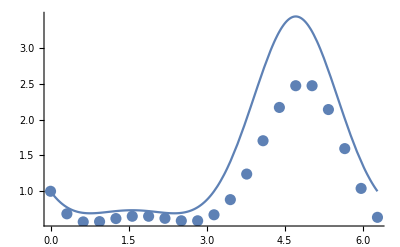

```mathematica
For[i=0,i≤n,i=i+1,yy[i+1]=yy[i]+h f[xx[i],yy[i]]]
puntos=Table[{xx[i],yy[i]},{i,0,n}];
Show[ListPlot[puntos,PlotStyle->PointSize[0.02]],Plot[-1+2 ⅇ^(-Sin[x])+Sin[x],{x,0,2Pi}],PlotRange->All]
```

### Métodos de Taylor (segundo orden)

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_,y_]:=Sin[x]*Cos[x]-y*Cos[x]
seg[x_,y_]:=D[f[x,y],x]+D[f[x,y],y]f[x,y]//Simplify
a=0.;
b=2π;
yy[0]=1;
n=40;
h=(b-a)/n;
xx[i_]:= a+i* h
```

Escribimos la formula de Taylor :

```mathematica
For[i=0,i≤n,i=i+1,yy[i+1]=yy[i]+h f[xx[i],yy[i]]+h^2/2 seg[xx[i],yy[i]]]
```

```mathematica
puntos=Table[{xx[i],yy[i]},{i,0,n}];
```

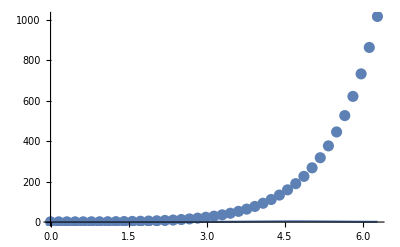

```mathematica
Show[ListPlot[puntos,PlotStyle->PointSize[0.02]],Plot[-1+2 ⅇ^(-Sin[x])+Sin[x],{x,0,2Pi}],PlotRange->All]
```

### Métodos de Taylor (tercer orden)

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_,y_]:=Sin[x]*Cos[x]-y*Cos[x]
D[f[x,y],x]+D[f[x,y],y]f[x,y]//Simplify
```

```mathematica
seg[x_,y_]:=Cos[x]^2 (1+y-Sin[x])+(y-Sin[x]) Sin[x]
```

```mathematica
D[seg[x,y],x]+D[seg[x,y],y]f[x,y]//Simplify
```

1/4 Cos[x] (4+2 y-2 (4+y) Cos[2 x]-3 (5+4 y) Sin[x]+Sin[3 x])

```mathematica
ter[x_,y_]:=1/4 Cos[x] (4+2 y-2 (4+y) Cos[2 x]-3 (5+4 y) Sin[x]+Sin[3 x])
a=0.;
b=2π;
yy[0]=1;
n=20;
h=(b-a)/n;
xx[i_]:= a+i* h
```

```mathematica
For[i=0,i≤n,i=i+1,yy[i+1]=yy[i]+h f[xx[i],yy[i]]+h^2/2 seg[xx[i],yy[i]]+h^3/(3!)ter[xx[i],yy[i]]]
```

```mathematica
puntos=Table[{xx[i],yy[i]},{i,0,n}];
```

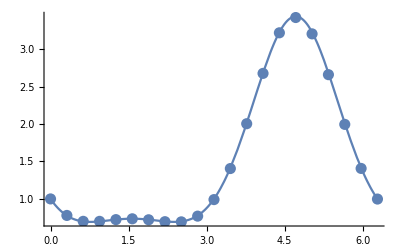

```mathematica
Show[ListPlot[puntos,PlotStyle->PointSize[0.02]],Plot[-1+2 ⅇ^(-Sin[x])+Sin[x],{x,0,2Pi}],PlotRange->All]
```

### Métodos de Runge-Kutta.

#### Métodos de Runge-Kutta (1)

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_,y_]:=Sin[x]* Cos[x]-y*Cos[x]
```

```mathematica
a=0.;
b=2Pi;
yy[0]=1;
n=20;
h=(b-a)/n;
xx[i_]:=a+i*h;
```

```mathematica
For[i=0,i≤n,i=i+1,
k[i,1]=f[xx[i],yy[i]];
k[i,2]=f[xx[i]+h/2,yy[i]+h/2 k[i,1]];
yy[i+1]=yy[i]+h k[i,2] ]
```

```mathematica
puntos=Table[{xx[i],yy[i]},{i,0,n}];
```

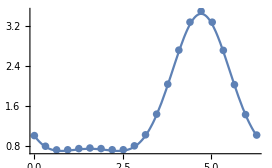

```mathematica
Show[ListPlot[puntos,PlotStyle->PointSize[0.02]],Plot[-1+2 ⅇ^(-Sin[x])+Sin[x],{x,0,2Pi}],PlotRange->All]
```

#### Métodos de Runge-Kutta (2)

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_,y_]:=Sin[x]* Cos[x]-y*Cos[x]
```

```mathematica
a=0.;
b=2Pi;
yy[0]=1;
n=5000;
h=(b-a)/n;
xx[i_]:=a+i*h;
```

```mathematica
For[i=0,i≤n,i=i+1,
k[i,1]=f[xx[i],yy[i]];
k[i,2]=f[xx[i]+h,yy[i]+h k[i,1]];
yy[i+1]=yy[i]+h/2 (k[i,1]+k[i,2])]
```

```mathematica
puntos=Table[{xx[i],yy[i]},{i,0,n}]
```

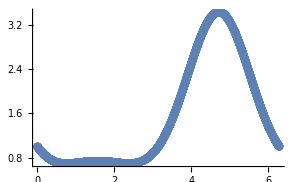

```mathematica
Show[ListPlot[puntos,PlotStyle->PointSize[0.02]],Plot[-1+2 ⅇ^(-Sin[x])+Sin[x],{x,0,2Pi}],PlotRange->All]
```

#### Métodos de Runge-Kutta (3)

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_,y_]:=Sin[x]* Cos[x]-y*Cos[x]
```

```mathematica
a=0.;
b=2Pi;
yy[0]=1;
n=40;
h=(b-a)/n;
xx[i_]:=a+i*h;
```

```mathematica
For[i=0,i≤n,i=i+1,
k[i,1]=f[xx[i],yy[i]];

k[i,2]=f[xx[i]+h/2,yy[i]+h/2 k[i,1]];

k[i,3]=f[xx[i]+h/2,yy[i]+h/2 k[i,2]];

k[i,4]=f[xx[i]+h,yy[i]+h k[i,3]];
yy[i+1]=yy[i]+h/6 (k[i,1]+2k[i,2]+2k[i,3]+k[i,4 ])]
```

```mathematica
yy[n]
```

1.

```mathematica
sol[x_]:=-1+2 ⅇ^(-Sin[x])+Sin[x]
```

```mathematica
puntos=Table[sol[xx[i]],{i,0,n}]
```

{1.,0.86681,0.777354,0.724168,0.698898,0.693244,0.699608,0.711492,0.723722,0.732562,0.735759,0.732562,0.723722,0.711492,0.699608,0.693244,0.698898,0.724168,0.777354,0.86681,1.,1.18223,1.41515,1.69518,2.01221,2.34912,2.68238,2.98416,3.22583,3.38235,3.43656,3.38235,3.22583,2.98416,2.68238,2.34912,2.01221,1.69518,1.41515,1.18223,1.}

```mathematica
puntos=Table[{xx[i],yy[i]},{i,0,n}]
```

{{0.,1},{0.15708,1.00134},{0.314159,1.0112},{0.471239,1.03941},{0.628319,1.09749},{0.785398,1.19891},{0.942478,1.35944},{1.09956,1.59753},{1.25664,1.93475},{1.41372,2.39637},{1.5708,3.01194},{1.72788,3.81603},{1.88496,4.84911},{2.04204,6.15851},{2.19911,7.79964},{2.35619,9.8373},{2.51327,12.3473},{2.67035,15.4185},{2.82743,19.1546},{2.98451,23.6771},{3.14159,29.1282},{3.29867,35.6743},{3.45575,43.5099},{3.61283,52.8628},{3.76991,63.9994},{3.92699,77.2316},{4.08407,92.9242},{4.24115,111.504},{4.39823,133.47},{4.55531,159.408},{4.71239,190.001},{4.86947,226.049},{5.02655,268.488},{5.18363,318.414},{5.34071,377.109},{5.49779,446.072},{5.65487,527.059},{5.81195,622.122},{5.96903,733.666},{6.12611,864.5},{6.28319,1017.91}}

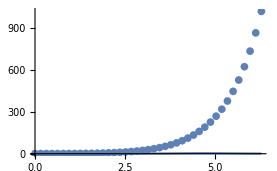

```mathematica
Show[ListPlot[puntos,PlotStyle->PointSize[0.02]],Plot[-1+2 ⅇ^(-Sin[x])+Sin[x],{x,0,2Pi}],PlotRange->All]
```

Comparativa de los métodos vistos. Colocamos los valores que hemos obtenidos por los distintos métodos con n=20.

```mathematica
Transpose[{{0.,0.3141592653589793,0.6283185307179586,0.9424777960769379,1.2566370614359172,1.5707963267948966,1.8849555921538759,2.199114857512855,2.5132741228718345,2.827433388230814,3.141592653589793,3.4557519189487724,3.7699111843077517,4.084070449666731,4.39822971502571,4.71238898038469,5.026548245743669,5.340707511102648,5.654866776461628,5.969026041820607,6.283185307179586},{1,0.6858407346410207,0.5732521254805015,0.5769458676740765,0.6197997002688043,0.6519582948012947,0.6519582948012947,0.6229216743755132,0.5885576507104869,0.5887539636350062,0.6723346750772585,0.883554842674898,1.2398752920251435,1.7043938333838549,2.1685157100935935,2.4713655036364823,2.4713655036364823,2.1391148849826638,1.594718208751519,1.0400127261680363,0.6369452871449723},{1,0.7845367786519143,0.7155716948206107,0.7232260832617722,0.7512296585518828,0.7650212039848584,0.7534254651882898,0.7287449800563701,0.7263981037750422,0.8024242961418349,1.0240295590711432,1.4456197882755306,2.0660738468013453,2.7816161212120276,3.3795728511815466,3.6218639750004304,3.393784129855928,2.7932558299908337,2.062717370777326,1.4300910388792434,1.0062164508493063},{1,0.7793690658718643,0.7007145148234463,0.7004562454819593,0.7235300883221748,0.734579452947322,0.7214814739506686,0.6960444477496329,0.6936094689693244,0.7700278259877543,0.9908993491602389,1.4056142184101494,2.004211862154386,2.676339158322766,3.2183171828280535,3.422338968539679,3.2041052878046385,2.659336992266867,1.9953784310682596,1.407055805757729,0.9981218878222726},{1,0.786989298449351,0.7137645115871185,0.7158419426703155,0.7395978749535275,0.7512859238457433,0.7396678474982634,0.7166196609463478,0.7168377882616985,0.7950041205141217,1.0156747236633277,1.4288746350496386,2.0285964913477614,2.710177675864107,3.270140128299989,3.48946232528889,3.269431248743035,2.7052662149399875,2.0193067661029502,1.4197259293245974,1.0107926160320393},{1,0.7866260627402508,0.7081410965158943,0.7049843605773023,0.7256015276297544,0.736545174997966,0.7261327352931054,0.705546171914894,0.7085297878839062,0.788142470762418,1.0060076060181715,1.4076992625816607,1.9829313055102378,2.6277216619964823,3.1495522232826993,3.348596903139162,3.139890539592478,2.6133844231899195,1.9709036401947027,1.402296088082819,1.006684762654146},{1,0.7773818379252144,0.6989305962587367,0.6996448985576348,0.7237677755806863,0.7358097719036916,0.7237680201227807,0.6996463828348961,0.6989332269895044,0.7773882290124129,1.0000211701409907,1.4151374055281702,2.0121390367934477,2.6822609603192475,3.225675594452896,3.4363992103251326,3.225673298765985,2.6822449124859586,2.0121106674946576,1.4151161196775668,1.0000178506335948},{1.,0.7773535807529408,0.6988979329709661,0.6996081527909879,0.723721798356248,0.7357588823428847,0.7237217983562481,0.6996081527909879,0.698897932970966,0.7773535807529408,0.9999999999999999,1.4151540418225264,2.012209662316393,2.6823817380290365,3.2258293783705794,3.43656365691809,3.2258293783705803,2.6823817380290373,2.012209662316394,1.4151540418225268,1.0000000000000002}}]//MatrixForm
```

(0. | 1 | 1 | 1 | 1 | 1 | 1 | 1.
0.314159 | 0.685841 | 0.784537 | 0.779369 | 0.786989 | 0.786626 | 0.777382 | 0.777354
0.628319 | 0.573252 | 0.715572 | 0.700715 | 0.713765 | 0.708141 | 0.698931 | 0.698898
0.942478 | 0.576946 | 0.723226 | 0.700456 | 0.715842 | 0.704984 | 0.699645 | 0.699608
1.25664 | 0.6198 | 0.75123 | 0.72353 | 0.739598 | 0.725602 | 0.723768 | 0.723722
1.5708 | 0.651958 | 0.765021 | 0.734579 | 0.751286 | 0.736545 | 0.73581 | 0.735759
1.88496 | 0.651958 | 0.753425 | 0.721481 | 0.739668 | 0.726133 | 0.723768 | 0.723722
2.19911 | 0.622922 | 0.728745 | 0.696044 | 0.71662 | 0.705546 | 0.699646 | 0.699608
2.51327 | 0.588558 | 0.726398 | 0.693609 | 0.716838 | 0.70853 | 0.698933 | 0.698898
2.82743 | 0.588754 | 0.802424 | 0.770028 | 0.795004 | 0.788142 | 0.777388 | 0.777354
3.14159 | 0.672335 | 1.02403 | 0.990899 | 1.01567 | 1.00601 | 1.00002 | 1.
3.45575 | 0.883555 | 1.44562 | 1.40561 | 1.42887 | 1.4077 | 1.41514 | 1.41515
3.76991 | 1.23988 | 2.06607 | 2.00421 | 2.0286 | 1.98293 | 2.01214 | 2.01221
4.08407 | 1.70439 | 2.78162 | 2.67634 | 2.71018 | 2.62772 | 2.68226 | 2.68238
4.39823 | 2.16852 | 3.37957 | 3.21832 | 3.27014 | 3.14955 | 3.22568 | 3.22583
4.71239 | 2.47137 | 3.62186 | 3.42234 | 3.48946 | 3.3486 | 3.4364 | 3.43656
5.02655 | 2.47137 | 3.39378 | 3.20411 | 3.26943 | 3.13989 | 3.22567 | 3.22583
5.34071 | 2.13911 | 2.79326 | 2.65934 | 2.70527 | 2.61338 | 2.68224 | 2.68238
5.65487 | 1.59472 | 2.06272 | 1.99538 | 2.01931 | 1.9709 | 2.01211 | 2.01221
5.96903 | 1.04001 | 1.43009 | 1.40706 | 1.41973 | 1.4023 | 1.41512 | 1.41515
6.28319 | 0.636945 | 1.00622 | 0.998122 | 1.01079 | 1.00668 | 1.00002 | 1.)

En la primera columna aparecen los puntos (de 0 a 2π) y en la última los valores exactos de la solución. El resto de columnas, de izquierda a derecha, son: los valores de Euler, Taylor de segundo orden, Taylor de tercer orden, Runge-Kutta en el punto medio, Runge-Kutta en los extremos y Runge-Kutta clásico. Este último método da los valores más próximos a la solución, aunque es el que más evaluaciones de f realiza.

### Ejercicios :

#### 1. Calcular una aproximación de la solución y (x), de la ecuación diferencial y' = x^2 + y + 1 con la condición y (0) = 1, en el punto 1, utilizando el método de Runge-Kutta con paso h = 0.5 .

y' = f (x, y) (en este caso f (x, y) = x^2 + y^2), y (x0) = y0 (en este caso x0 = 0, y0 = 1)
yn + 1 = yn + 1/6 h (k1 + 2 k2 + 2 k3 + k4)
Donde
k1=f(xn,yn)
k2=f(xn+1/2 h,yn+1/2 k1h)
k3=f(xn+1/2 h,yn+1/2 k2h)
k4=f(xn+h,yn+k3h)

```mathematica
Clear[f,x]
```

```mathematica
f[x_,y_]:=x^2+y+1
x0=0;
y0=1;h=0.5;Do[k1=f[x0,y0];k2=f[x0+h/2,y0+k1 h/2];k3=f[x0+h/2,y0+k2 h/2];k4=f[x0+h,y0+k3 h];y0=y0+h(k1+2k2+2k3+k4)/6; x0=x0+h;Print["En " ,x0," vale aprox. ",y0],{2}]

"En "0.5" vale aprox. "2.3444010416666665
"En "1." vale aprox. "4.8711090087890625
```

En 0.5 vale aprox. 2.3444

En 1. vale aprox. 4.87111

En 0.5 vale aprox. 2.3444

En 1. vale aprox. 4.87111

#### 2.- Realizar cuatro iteraciones por el método de la secante para aproximar la solución de la ecuación x^3 - ⅇ^x=0 partiendo de x_0=0, x_1=1. El noveno decimal de x_5 es: 1) 7, 2) 8, 3) 6, 4) 2, 5) 4

```mathematica
Clear["Global`*"]
```

```mathematica
h[x_]:=x^3-E^x
```

```mathematica
s0=0;s1=1;s2=(s1*h[s0]-s0*h[s1])/(h[s0]-h[s1]);s3=(s2*h[s1]-s1*h[s2])/(h[s1]-h[s2]);s4=(s3*h[s2]-s2*h[s3])/(h[s2]-h[s3]);s5=(s4*h[s3]-s3*h[s4])/(h[s3]-h[s4]);N[{s0,s1,s2,s3,s4,s5},15]
```

{0,1.,-1.39221119117733,4.34540150685833,0.754620060661719,1.67428193835979}

#### 3. Aproximar el valor de la integral ∫_0^1 1/(1+x+2 x^2)ⅆx utilizando la fórmula del punto medio compuesta partiendo en 20 trozos iguales el intervalo [0,1]. El octavo decimal de la aproximación es: 1) 3, 2) 2, 3) 4, 4) 7, 5) 8

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]:=1/(1+x+2 x^2)
```

```mathematica
a=0; b=1;n=20; xx=Table[a+i(b-a)/n,{i,0,n}];
```

```mathematica
N[(b-a)1/n∑_(i=1)^n f[(xx[[i]]+xx[[i+1]])/2],20]
```

0.54626397858853200174

## Tema 11

#### 1. Realiza cinco iteraciones por el método de Newton para aproximar la solución de la ecuación x^3+2x + coseno x =0 partiendo de x0=-2. Escribir x5 con 12 cifras decimales

```mathematica
Clear[f,x]
```

```mathematica
f[x_]:=x^3+2x+Cos[x]
```

```mathematica
f'[x]
```

2+3 x^2-Sin[x]

```mathematica
x=-2;
Do[x=x-f[x]/f'[x];
Print[N[x,12]],{5}];
Print["Una aproximacion seria ", N[x,12]," .La funcion vale " , N[f[x],12]]
```

-1.16722119889

-0.663150544281

-0.452249271241

-0.420278167268

-0.419659987914

Una aproximacion seria -0.419659987914 .La funcion vale -6.56047157627×10^-7

#### 2. Realiza cinco interacciones por el método de la secante para aproximar la solución de la ecuación x^3+x+1=0 partiendo de x0=-2, x1=-1. Escribir x5 con 10 cifras decimales.

```mathematica
Clear[f,x]
```

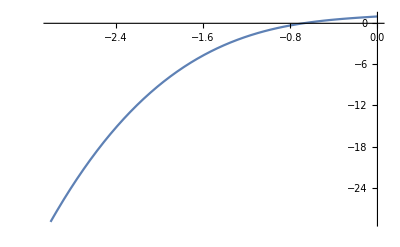

Una aproximacion seria -0.6823290863.La funcion vale -3.073648154×10^-6

```mathematica
f[x_]:=x^3+x+1
Plot[x^3+x+1,{x,-3,0}]
a=-2;
b=-1;
Do[c=b;b=(a f[b]-b f[a])/(f[b]-f[a]);a=c,{5}];
Print["Una aproximacion seria ",N[b,10],".La funcion vale ",N[f[b],10]]
```

## Tema 12

#### Deducción de fórmulas

Fórmulas con un punto

```mathematica
InterpolatingPolynomial[{{a,fa}},x]
```

fa

```mathematica
∫_a^b faⅆx
```

(-a+b) fa

```mathematica
InterpolatingPolynomial[{{b,fb}},x]
```

fb

```mathematica
∫_a^b fbⅆx
```

(-a+b) fb

```mathematica
InterpolatingPolynomial[{{(a+b)/2,fm}},x]
```

fm

```mathematica
∫_a^b fmⅆx
```

(-a+b) fm

```mathematica
InterpolatingPolynomial[{{a,fa},{b,fb}},x]
```

fa+((-fa+fb) (-a+x))/(-a+b)

```mathematica
∫_a^b (fa+((-fa+fb) (-a+x))/(-a+b))ⅆx
```

-1/2 (a-b) (fa+fb)

```mathematica
InterpolatingPolynomial[{{a,fa},{b,fb},{(a+b)/2,fm}},x]//Simplify
```

1/(a-b)^2(b^2 fa+a^2 fb+a b (fa+fb-4 fm)-b (3 fa+fb-4 fm) x-a (fa+3 fb-4 fm) x+2 (fa+fb-2 fm) x^2)

```mathematica
∫_a^b (1/(a-b)^2(b^2 fa+a^2 fb+a b (fa+fb-4 fm)-b (3 fa+fb-4 fm) x-a (fa+3 fb-4 fm) x+2 (fa+fb-2 fm) x^2))ⅆx
```

-1/6 (a-b) (fa+fb+4 fm)

```mathematica
InterpolatingPolynomial[{{a,fa},{b,fb},{(2a+b)/3,fm1},{(a+2b)/3,fm2}},x]//Simplify
```

1/(2 (a-b)^3)(-2 b^3 fa+2 a^3 fb+b^2 (11 fa-2 fb-18 fm1+9 fm2) x-9 b (2 fa-fb-5 fm1+4 fm2) x^2+9 (fa-fb-3 fm1+3 fm2) x^3+a^2 (b (-2 fa+5 fb+9 fm1-18 fm2)+(2 fa-11 fb-9 fm1+18 fm2) x)+a (b^2 (-5 fa+2 fb+18 fm1-9 fm2)+2 b (7 fa-7 fb-27 fm1+27 fm2) x-9 (fa-2 fb-4 fm1+5 fm2) x^2))

```mathematica
∫_a^b (1/(2 (a-b)^3)(-2 b^3 fa+2 a^3 fb+b^2 (11 fa-2 fb-18 fm1+9 fm2) x-9 b (2 fa-fb-5 fm1+4 fm2) x^2+9 (fa-fb-3 fm1+3 fm2) x^3+a^2 (b (-2 fa+5 fb+9 fm1-18 fm2)+(2 fa-11 fb-9 fm1+18 fm2) x)+a (b^2 (-5 fa+2 fb+18 fm1-9 fm2)+2 b (7 fa-7 fb-27 fm1+27 fm2) x-9 (fa-2 fb-4 fm1+5 fm2) x^2)))ⅆx//Simplify
```

-1/8 (a-b) (fa+fb+3 (fm1+fm2))

```mathematica
∫1/Log[x] ⅆx
```

LogIntegral[x]

```mathematica
∫ⅇ^(x^2)ⅆx
```

1/2 √π Erfi[x]

```mathematica
∫1/(x^5-x^3+1)ⅆx
```

RootSum[1-#1^3+#1^5&,Log[x-#1]/(-3 #1^2+5 #1^4)&]

Limpiamos todas las variables

```mathematica
ClearAll
```

ClearAll

```mathematica
Clear[f, x, a, b, n, xx]
```

FORMULA DE SIMPSON

```mathematica
f[x_]:=1/Log[x]
a=6;
b=7;
recizq=f[a](b-a);
recder= f[b](b-a);
puntmed=f[(a+b)/2](b-a);
trap=((f[a]+f[b])/2)(b-a);
simp=((f[a]+4f[(a+b)/2]+f[b])/6)(b-a);
{∫_a^b f[x]ⅆx,recizq,recder,puntmed,trap,simp}//N
```

{0.534829,0.558111,0.513898,0.534244,0.536004,0.534831}

```mathematica
Total[{0.5348293754585036,0.5581106265512472,0.5138983423697507,0.5342444903314023,0.536004484460499,0.5348311550411011}]
```

3.21192

NOS DAN LOS VALORES DE LO QUE VALE CADA UNO

```mathematica
{recizq -∫_a^b f[x]ⅆx,recder-∫_a^b f[x]ⅆx,puntmed -∫_a^b f[x]ⅆx ,trap-∫_a^b f[x]ⅆx ,simp-∫_a^b f[x]ⅆx}//N
```

{0.0232813,-0.020931,-0.000584885,0.00117511,1.77958×10^-6}

EL ERROR DE CADA VALOR ; EL MAS PRECISO EN ESTE CASO ES SIMP

```mathematica
n=100;
xx=Table[a+i(b-a)/n,{i,0,n}];
xx
```

{6,601/100,301/50,603/100,151/25,121/20,303/50,607/100,152/25,609/100,61/10,611/100,153/25,613/100,307/50,123/20,154/25,617/100,309/50,619/100,31/5,621/100,311/50,623/100,156/25,25/4,313/50,627/100,157/25,629/100,63/10,631/100,158/25,633/100,317/50,127/20,159/25,637/100,319/50,639/100,32/5,641/100,321/50,643/100,161/25,129/20,323/50,647/100,162/25,649/100,13/2,651/100,163/25,653/100,327/50,131/20,164/25,657/100,329/50,659/100,33/5,661/100,331/50,663/100,166/25,133/20,333/50,667/100,167/25,669/100,67/10,671/100,168/25,673/100,337/50,27/4,169/25,677/100,339/50,679/100,34/5,681/100,341/50,683/100,171/25,137/20,343/50,687/100,172/25,689/100,69/10,691/100,173/25,693/100,347/50,139/20,174/25,697/100,349/50,699/100,7}

```mathematica
xx[[11]]
```

7

```mathematica
recizqC=(b-a) 1/n∑_(i=1)^n f[xx[[i]]];
recderC= (b-a) 1/n∑_(i=1)^n f[xx[[i+1]]];
puntmedC=(b-a) 1/n∑_(i=1)^n f[(xx[[i]]+xx[[i+1]])/2];
trapC=(b-a) 1/n∑_(i=1)^n ((f[xx[[i]]]+f[xx[[i+1]]])/2);
simpC=(b-a) 1/n∑_(i=1)^n ((f[xx[[i]]]+4*f[(xx[[i]]+xx[[i+1]])/2]+f[xx[[i+1]]])/6);
{∫_a^b f[x]ⅆx,recizqC,recderC,puntmedC,trapC,simpC}//N
```

{0.534829,0.535051,0.534608,0.534829,0.534829,0.534829}

```mathematica
{recizq -∫_a^b f[x]ⅆx,recderC-∫_a^b f[x]ⅆx,puntmedC-∫_a^b f[x]ⅆx ,trapC-∫_a^b f[x]ⅆx ,simpC-∫_a^b f[x]ⅆx}//N
```

{0.0232813,-0.000220943,-5.91134×10^-8,1.18227×10^-7,1.95399×10^-14}

EL ERROR DE CADA VALOR ; EL MAS PRECISO EN ESTE CASO ES SIMP

```mathematica
{N[simpC,35],N[∫_a^b f[x]ⅆx,35]}
```

{0.53482937545852317806694785341771718,0.53482937545850486448883730316314878}

```mathematica
ClearAll
```

ClearAll

#### Ejercicio 2018

```mathematica
f[x_]:=4/(1+x^2)
a=0;
b=1;
n=10;
xx=Table[a+i(b-a)/n,{i,0,n}];
xx
recizqC=(b-a) 1/n∑_(i=1)^n f[xx[[i]]];
recderC= (b-a) 1/n∑_(i=1)^n f[xx[[i+1]]];
puntmedC=(b-a) 1/n∑_(i=1)^n f[(xx[[i]]+xx[[i+1]])/2];
trapC=(b-a) 1/n∑_(i=1)^n ((f[xx[[i]]]+f[xx[[i+1]]])/2);
simpC=(b-a) 1/n∑_(i=1)^n ((f[xx[[i]]]+4*f[(xx[[i]]+xx[[i+1]])/2]+f[xx[[i+1]]])/6)
N[simpC,15]
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}

5988585315838311774901484536676836463/1906225910662615880075423535413820750

3.14159265296978

```mathematica
N[Pi,20]
```

3.1415926535897932385

```mathematica
ClearAll
```

ClearAll

#### Ejercicio de Enero del 2019

```mathematica
f[x_]:=1/(1+x+x^2)
a=0;
b=1;
n=10;
xx=Table[a+i(b-a)/n,{i,0,n}];
xx
recizqC=(b-a) 1/n∑_(i=1)^n f[xx[[i]]];
recderC= (b-a) 1/n∑_(i=1)^n f[xx[[i+1]]];
puntmedC=(b-a) 1/n∑_(i=1)^n f[(xx[[i]]+xx[[i+1]])/2];
trapC=(b-a) 1/n∑_(i=1)^n ((f[xx[[i]]]+f[xx[[i+1]]])/2)
simpC=(b-a) 1/n∑_(i=1)^n ((f[xx[[i]]]+4*f[(xx[[i]]+xx[[i+1]])/2]+f[xx[[i+1]]])/6);
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}

1112495934470107/1838361412596345

```mathematica
N[trapC,10]
```

0.6051562695

Comprobar el error

```mathematica
N[trapC-∫_a^b f[x]ⅆx,10]
```

0.0005564814385

## EJERCICIOS VARIADOS DE DISTINTOS TEMAS Y DISTINTOS AÑOS

### 2.Calcular el área de la superficie obtenida al girar la gráfica de la función f(x)=√(1+x)-1cos x en [0,2] alrededor del eje horizontal

```mathematica
2π∫_0^2 f[x] √(1+(f'[x])^2)ⅆx
f[x_]:=-1+√(1+x)
f'[x]//Simplify
g[x_]:=(f'[x])^2
g[x]
2π∫_0^2 f[x] √(1+g[x])ⅆx
2π∫_0^2 f[x] √(1+g[x])ⅆx //N
```

2 π ∫_0^2 (√(1+x)-Cos[x]) √(1+(1/(2 √(1+x))+Sin[x])^2)ⅆx

1/(2 √(1+x))

1/(4 (1+x))

1/6 π (√5+13 √13-6 √39+3 ArcSinh[2]-3 ArcSinh[2 √3])

5.28925

### 3.Calcular el volumen obtenido al girar la gráfica de la función f(x)=4-2x,con x en [0,2] alrededor del eje vertical y limitado por el plano horizontal

```mathematica
∫_0^2 2π x(4-2x)ⅆx//N
```

16.7552

### 4.Dado el problema de valores iniciales y’=2y(20-y) con y(0)=1,escribir y(0.1) con ocho cifras decimales

```mathematica
f=DSolve[{y'[x]==2 y[x](20-y[x]),y[0]==1},y[x],x]
```

{{y[x]→(20 ⅇ^(40 x))/(19+ⅇ^(40 x))}}

```mathematica
{{y[x]->(20 ⅇ^(40 x))/(19+ⅇ^(40 x))}}
```

{{y[x]→(20 ⅇ^(40 x))/(19+ⅇ^(40 x))}}

```mathematica
N[(20 ⅇ^4)/(19+ⅇ^4),10]
```

14.83682674

### 5.Dado el problema de valores iniciales y’=2y(10-y) con y(0)=1,escribir y(0.1) con ocho cifras decimales

```mathematica
Clear[g,x]
```

```mathematica
g=DSolve[{y'[x]==2y[x](10-y[x]),y[0]==1},y[x],x]
```

{{y[x]→(10 ⅇ^(20 x))/(9+ⅇ^(20 x))}}

```mathematica
N[(10 ⅇ^2)/(9+ⅇ^2),10]
```

4.508530604

```mathematica
Solucion=4.508506;
```

### 6.La temperatura de un cuerpo que se esta enfriando se aproxima por la solución de la ecuación diferencial solución=k(20-y), para una cierta constante k, sabiendo que y(0)=40 e y(2)=30, calcular y(5)

```mathematica
Clear[g,x,k]
```

```mathematica
g=DSolve[{y'[x] == k (20 - y[x]), y[0] == 40}, y[x], x]
```

{{y[x]→20 ⅇ^(-k x) (1+ⅇ^(k x))}}

```mathematica
g[2]
```

{{y[x]→20 ⅇ^(-k x) (1+ⅇ^(k x))}}[2]

```mathematica
NSolve[20 ⅇ^(-k 2) (1+ⅇ^(k 2))-30==0,k,Reals]
```

{{k→0.346574}}

```mathematica
k=0.346574;
g[5]
```

{{y[x]→20 ⅇ^(-0.346574 x) (1+ⅇ^(0.346574 x))}}[5]

```mathematica
20 ⅇ^(-0.346574 * 5) (1+ⅇ^(0.346574 * 5))
```

23.5355

### 7.Calcular la integral de la función f(x,y)=x^2+y^2 en el cuadrilátero de vertices (0,0),(1,0),(2,1),(1,1)

Tenemos que calcular la integral de la funcion f(x,y) en el dominio D={(x,y)/0 <=y <= 1 , y<=x<=y+1 } Luego los limites de la integral seran (0,1) para la variable y,(y,y+1) para la variable x

```mathematica
∫_0^1 ∫_y^(y+1) (x^2+y^2)ⅆxⅆy
```

3/2

### 8.Calcular la integral de la función f(x,y)=2x^2+y^2 en el cuadrilátero de vertices (0,0),(1,0),(2,1),(1,1)

Tenemos que calcular la integral de la funcion f (x, y) en el dominio D = {(x, y)/0 <= y <= 1 , y <= x <= y + 1 } Luego los limites de la integral seran (0, 1) para la variable y, (y, y + 1) para la variable x

```mathematica
∫_0^1 ∫_y^(y+1) (2x^2+y^2)ⅆxⅆy
```

8/3

### 9.Calcular la integral de la función f(x,y)=x^2+2y^2 en el cuadrilátero de vertices (0,0),(1,0),(2,1),(1,1)

Tenemos que calcular la integral de la funcion f (x, y) en el dominio D = {(x, y)/0 <= y <= 1 , y <= x <= y + 1 } Luego los limites de la integral seran (0, 1) para la variable y, (y, y + 1) para la variable x

```mathematica
∫_0^1 ∫_y^(y+1) (x^2+2y^2)ⅆxⅆy
```

11/6

### 10.Calcular la integral de la función f(x,y)=1-x-y en el triangulo de vertices (0,0),(1,0),(0,1) para obtener el volumen de la siguiente figura

Tenemos que calcular la integral de la funcion f (x, y) en el dominio D = {(x, y)/0<=x<=1,0<=y<=1-x } Luego los limites de la integral seran (0, 1) para la variable x, (0,1-x) para la variable y

```mathematica
∫_0^1 ∫_0^(1-x) (1-x-y)ⅆyⅆx
```

1/6

### 11.Realizar cinco iteraciones por el método de Newton para aproximar la solución de la ecuación x^3+2x +cos x =0 partiendo de x0=-2.Escribir x5 con 12 cifras decimales

```mathematica
Clear[f,x]
```

```mathematica
f[x_]:=x^3+2x+Cos[x]
```

```mathematica
f'[x]
```

2+3 x^2-Sin[x]

```mathematica
x=-2;
Do[x=x-f[x]/f'[x];
Print[N[x,12]],{5}];
Print["Una aproximacion seria ", N[x,12]," .La funcion vale " , N[f[x],12]]
```

-1.16722119889

-0.663150544281

-0.452249271241

-0.420278167268

-0.419659987914

Una aproximacion seria -0.419659987914 .La funcion vale -6.56047157627×10^-7

### 12.Calcular una aproximación de la integral de ∫_1^2 1/(1+x+x^2)ⅆx utilizando la formula de Simpson compuesta haciendo 5 trozos en el intervalo [1,2]

```mathematica
Clear[f,x]
f[x_]:=1/(1+x+x^2)
a=1;
b=2;
n=5;
xx=Table[a+i(b-a)/n,{i,0,n}];
simpC=(b-a)1/n ∑_(i=1)^n 1/6(f[xx[[i]]]+4f[(xx[[i]]+xx[[i+1]])/2]+f[xx[[i+1]]]);
N[{∫_a^b f[x]ⅆx,simpC},10]
```

{0.2195381365,0.2195384308}

### 13.Calcular una aproximación de la integral de ∫_0^1 1/(1+x+x^2)ⅆx utilizando la formula del trapecio compuesta haciendo 10 trozos en el intervalo [0,1]

```mathematica
Clear[f,x,a,b,n,xx]
f[x_]:=1/(1+x+x^2)
a=0;
b=1;
n=10;
xx=Table[a+i(b-a)/n,{i,0,n}];
trapC=(b-a)/n∑_(i=1)^n (f[xx[[i]]]+f[xx[[i+1]]])/2;
N[{∫_a^b f[x]ⅆx,trapC},10]
```

{0.6045997881,0.6051562695}

### 14.Calcular una aproximación de la solución y(x), de la ecuación diferencial y’=x^2+y+1 con la condición y(0)=1, en el punto 1, utilizando el método de Runge-Kutta con paso h=0.5.

y' = f (x, y) (en este caso f (x, y)=x^2+y^2),y(x0)=y0(en este caso x0=0,y0=1)
yn+1=yn+1/6h(k1+2k2+2k3+k4)
Donde
k1=f(xn,yn)
k2=f(xn+1/2 h,yn+1/2 k1h)
k3=f(xn+1/2 h,yn+1/2 k2h)
k4=f(xn+h,yn+k3h)

```mathematica
Clear[f,x]
f[x_,y_]:=x^2+y+1
x0=0;
y0=1;h=0.5;Do[k1=f[x0,y0];k2=f[x0+h/2,y0+k1 h/2];k3=f[x0+h/2,y0+k2 h/2];k4=f[x0+h,y0+k3 h];y0=y0+h(k1+2k2+2k3+k4)/6; x0=x0+h;Print["En " ,x0," vale aprox. ",y0],{2}]
```

En 0.5 vale aprox. 2.3444

En 1. vale aprox. 4.87111

### 15.Calcular el volumen obtenido al girar la gráfica de la función f(x)= 2+sen(πx) con x en [0,3] alrededor del eje horizontal

El volumen obtenido al girar respecto al eje horizontal 0X es la integral ∫_a^b π f^2(x)ⅆx

```mathematica
∫_0^3 π(2+Sin[π x])^2ⅆx
```

8+(27 π)/2

```mathematica
N[%]
```

50.4115

### 16.Una sustancia radiactiva se esta desintegrando según la ecuación diferencial y’=-K y, para una cierta constante K sabiendo que y(0)=40 e y(2)=20, calcular y(6)

La solucion de la ecuacion diferencial y’=-k y es y(x)= C ⅇ^(-kx) con C numero real. Imponiendo que y(0) sea 40, tenemos que C=40. Como y(2) debe ser 20 tenemos que y(2)=40 , e^(-2K)=20.Despejamos:ⅇ^(-2K)=1/2.Tomamos logaritmos, -2K =ln(1/2). K= (-ln(1/2))/2. Por tanto, y(x)=40 ⅇ^(-Kx)=40(1/2)^(x/2). Evaluando en x=6 , y(6)=40 (1/2)^(6/2)

```mathematica
40(1/2)^3
```

5

### 17.Calcular la integral de la función f(x,y)=x^2+y^2 en el triangulo de vertices (0,0),(1,0) y (1,1) para obtener el volumen de la siguiente figura

El conjunto donde tenemos que realizaar la integral es el triangulo de vertices (0,0),(1,0) y (1,1)

```mathematica
RegionPlot[0<= x <= 1 && 0<= y <= x ,{x,0,1}, {y,0,1}, AspectRatio ->Automatic]
```

-Graphics-

En este caso, podemos considerar una caulquiera de las variables, por ejemplo la x. La variable x se mueve entre 0 y 1. Una vez fijado el valor de x, entre 0 y 1. El valor de y se movera entre 0 y x. La variable y se movera desdde 0 hasta el punto de la recta que une (0,0) y (1,1). Se trara de la recta y=x

```mathematica
∫_0^1 ∫_0^x (x^2+y^2)ⅆyⅆx
```

1/3